### Análisis para el reconocimiento de numero de conexiones promedio. Redes generadas con configuración:

```mathematica
numPeople=1000;
```

```mathematica
limCapacity=5;
```

```mathematica
stopTime=26000;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Carga de 20 redes con la configuración anterior.

```mathematica
redes=Table[Import[StringJoin["integration-network-1000-26000-",IntegerString[i],".g6"]],{i,1,20,1}];
```

```mathematica
avgClusteringRedes=Map[MeanClusteringCoefficient,Flatten[redes,1]];
```

```mathematica
aplRedes=Map[MeanGraphDistance,Flatten[redes,1]];
```

```mathematica
avgEdgesCountRedes=Map[EdgeCount,redes];
```

### Coeficiente de agrupamiento promedio de la configuración

```mathematica
N[Mean[avgClusteringRedes]]
```

0.267113

### Desviación estandar del coeficiente de agrupamiento promedio

```mathematica
N[StandardDeviation[avgClusteringRedes]]
```

0.00287239

### Longitud de camino promedio de la configuración

```mathematica
N[Mean[aplRedes]]
```

1.84642

### Desviación estandar de la longitud de camino promedio

```mathematica
N[StandardDeviation[aplRedes]]
```

0.00244772

### Promedio de conexiones o enlaces

```mathematica
avgConnections=Round[Mean[avgEdgesCountRedes]]
```

77758

### Desviación estandar del número de conexiones

```mathematica
Round[StandardDeviation[avgEdgesCountRedes]]
```

1216

### Carga de Redes Aleatorias

```mathematica
aleatorias=RandomGraph[{numPeople,avgConnections},20];
```

```mathematica
avgCCAleatorias=Map[MeanClusteringCoefficient,Flatten[aleatorias,1]];
```

```mathematica
aplAleatorias=Map[MeanGraphDistance,Flatten[aleatorias,1]];
```

### Average Clustering Coeff

```mathematica
N[Mean[avgCCAleatorias]]
```

0.15569

### Average Path Length

```mathematica
N[Mean[aplAleatorias]]
```

1.84433

## Análisis de ciclos

Función que recibe como entrada un grafo y devuelve la cantidad de ciclos de longitud 3 presentes en él

```mathematica
nGC3[g_]:=Module[{adjmatrix,matrix3,amountResult},
adjmatrix=AdjacencyMatrix[g];
matrix3=MatrixPower[adjmatrix,3];
amountResult=Tr[matrix3]/6;
Return[amountResult]
];
```

```mathematica
ciclos3=Map[nGC3,redes];
```

```mathematica
N[Mean[ciclos3]]
```

1.26451×10^6

```mathematica
ciclosAle3=Map[nGC3,aleatorias];
```

```mathematica
N[Mean[ciclosAle3]]
```

626959.

Función que recibe como entrada un grafo y encuentra la cantidad de ciclos de longitud 4

```mathematica
nGC4[g_]:=Module[{adjmatrix,matrix4, amountResult,sumatoria},
adjmatrix=AdjacencyMatrix[g];
matrix4=MatrixPower[adjmatrix,4];sumatoria=Sum[(VertexDegree[g,i]*(VertexDegree[g,i]-1)),{i,VertexCount[g]}];
amountResult=(Tr[matrix4]-(2*sumatoria)-(2*EdgeCount[g]))/8;
Return[amountResult]
];
```

```mathematica
ciclos4=Map[nGC4,redes];
```

```mathematica
N[Mean[ciclos4]]
```

1.74053×10^8

```mathematica
ciclosAle4=Map[nGC4,aleatorias];
```

```mathematica
N[Mean[ciclosAle4]]
```

7.29671×10^7

Función que recibe como entrada un grafo y encuentra la cantidad de ciclos de longitud 5

```mathematica
nGC5[g_]:=Module[{adjmatrix,matrix3,matrix5, amountResult,sumatoria},
adjmatrix=AdjacencyMatrix[g];
matrix3=MatrixPower[adjmatrix,3];
matrix5=MatrixPower[adjmatrix,5];sumatoria=Sum[matrix3[[i]][[i]]*(VertexDegree[g,i]-2),{i,VertexCount[g]}];
amountResult=(Tr[matrix5]-(5*sumatoria)-(5*Tr[matrix3]))/10;
Return[amountResult]
];
```

```mathematica
ciclos5=Map[nGC5,redes];
```

```mathematica
N[Mean[ciclos5]]
```

2.66531×10^10

```mathematica
ciclosAle5=Map[nGC5,aleatorias];
```

```mathematica
N[Mean[ciclosAle5]]
```

9.05075×10^9

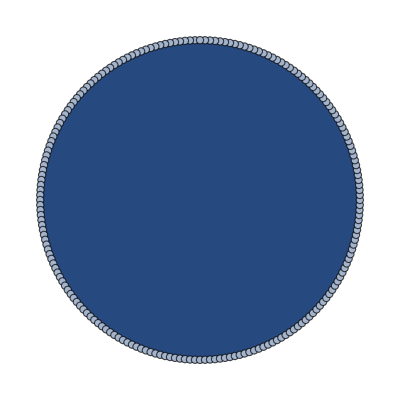

```mathematica
dodo=RandomGraph[{200,completo[200]}]
```

```mathematica
nGC3[dodo]
```

1313400

```mathematica
nGC4[dodo]
```

194054850

```mathematica
nGC5[dodo]
```

30427800480

```mathematica
completo[numnodos_]:=Module[{},
Return[(numnodos*(numnodos-1))/2];
];
```

```mathematica
completo[200]
```

19900